# WolframInstitute/NetworkSystem

Network Systems

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"CyclicNet.nb"DocumentationEnglishReferencePagesSymbolsCyclicNet.nb

"NetworkSystemDisplay.nb"DocumentationEnglishReferencePagesSymbolsNetworkSystemDisplay.nb

"NetworkSystemEvolutionList.nb"DocumentationEnglishReferencePagesSymbolsNetworkSystemEvolutionList.nb

"NetworkSystemEvolutionPlot.nb"DocumentationEnglishReferencePagesSymbolsNetworkSystemEvolutionPlot.nb

"NetworkSystemRule.nb"DocumentationEnglishReferencePagesSymbolsNetworkSystemRule.nb

"Tutorials"

"Kernel"

"NetworkSystemEvolution.m"KernelNetworkSystemEvolution.m

"NetworkSystem.m"KernelNetworkSystem.m

"NetworkSystemRules.m"KernelNetworkSystemRules.m

"LICENSE"LICENSE

"Notebooks"

"NetworkSystem-Dev.nb"NotebooksNetworkSystem-Dev.nb

"NetworkSystem-RulePost.nb"NotebooksNetworkSystem-RulePost.nb

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

A paragraph that describes your paclet in more detail.

### Details

Additional information about the paclet.

### Primary Context

WolframInstitute`NetworkSystem`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Get["WolframInstitute`NetworkSystem`"];
```

### Basic Examples

Get rules:

```mathematica
NetworkSystemRule[219,1]
```

{1,{{1}→{{2},{1}},{2}→{{1},{{1},{2}}}}}

Get initial net:

```mathematica
CyclicNet[5]
```

{{5,2},{1,3},{2,4},{3,5},{4,1}}

Get all state list:

```mathematica
NetworkSystemEvolutionList[NetworkSystemRule[219,1],CyclicNet[5],3]
```

{{{},{{5,2},{1,3},{2,4},{3,5},{4,1}}},{{1,1,2,2,3,3,4,4,5,5},{{9,2},{9,3},{1,4},{1,5},{3,6},{3,7},{5,8},{5,9},{7,10},{7,1}}},{{1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10},{{17,2},{17,3},{17,4},{17,5},{1,6},{1,7},{1,8},{1,9},{5,10},{5,11},{5,12},{5,13},{9,14},{9,15},{9,16},{9,17},{13,18},{13,19},{13,20},{13,1}}},{{1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11,11,12,12,13,13,14,14,15,15,16,16,17,17,18,18,19,19,20,20},{{33,2},{33,3},{33,4},{33,5},{33,6},{33,7},{33,8},{33,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{17,26},{17,27},{17,28},{17,29},{17,30},{17,31},{17,32},{17,33},{25,34},{25,35},{25,36},{25,37},{25,38},{25,39},{25,40},{25,1}}}}

Plot network evolution:

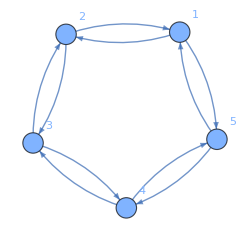
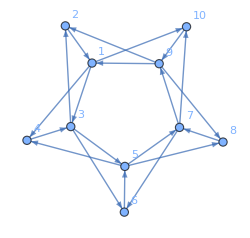
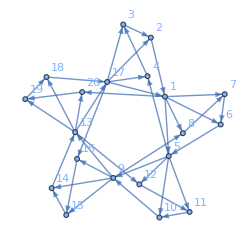
-Graphics--Graphics--Graphics--Graphics-

```mathematica
NetworkSystemEvolutionPlot[NetworkSystemRule[219,1],CyclicNet[5],2,"ImageSize"->Large,"GraphNetworkSize"->250]
```

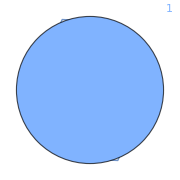
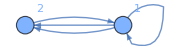
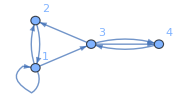
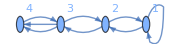
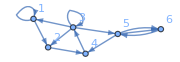
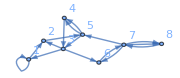
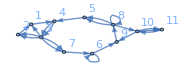
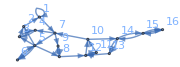
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{tot=15,
rule={2,{{1,1}->{{{},{1,1}},{2}},{1,2}->{{2},{{},{}}},{2,1}->{{2,1},{{},{1}}},{2,2}->{{{2},{1}},{}},{2,3}->{{1,2},{2}},{2,4}->{{{1},{1}},{2,1}}}}
},
NetworkSystemEvolutionPlot[rule,CyclicNet[1],tot,"GraphNetworkSize"->Small]
]
```

### Scope

Plot network for distance 2 starting from a initial condition of 3 nodes:

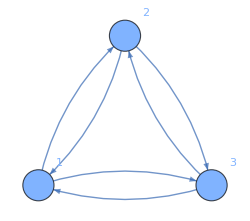
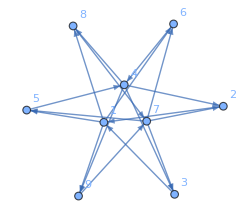
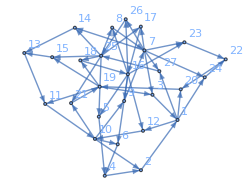
-Graphics--Graphics--Graphics--Graphics-

```mathematica
NetworkSystemEvolutionPlot[12472289834238,CyclicNet[3],2,"Depth"->2,"GraphNetworkSize"->250]
```

Network shown on NKS page198:

```mathematica
gridNet[i_,tot_]:={
Switch[Mod[i,4],
1,Mod[i-4+2,tot],
2,Mod[i-8+2,tot]/. 0->tot,
3,Mod[i+4-2,tot],
0,Mod[i+8-2,tot]
],i+If[Mod[i,4]==0,-2,1]
}
```

```mathematica
treeNet[tot_?OddQ]:=MapIndexed[#&,
Join[Partition[Range[2,tot],2],Table[{n,n},{n,(tot+1)/2,tot}]]]
```

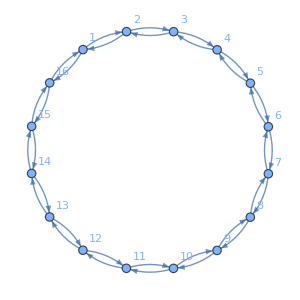
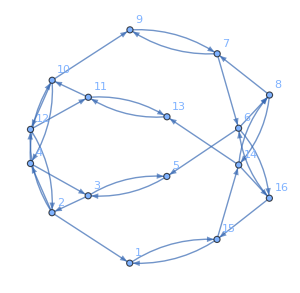
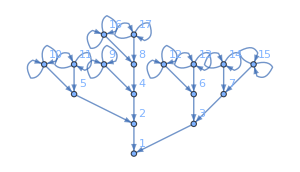

```mathematica
Module[{grid,tree,cyclic,tot=16},
cyclic=CyclicNet[tot];
tree=treeNet[tot+1];
grid=Table[gridNet[i,tot],{i,tot}];
Row[NetworkSystemDisplay[#,"ImageSize"->300]&/@{cyclic,grid,tree}]
]
```

## Source & Additional Information

### Creator

Brian A. Mboya

### Source Control Repository

https://github.com/asheux/NetworkSystem

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

network

graph

distant neighbour

neighbour dependent

node

enumeration

rule

depth

distance

cyclic

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Kate L. Morrow,1 Todd Rowland,2 and Christopher M. Danforth (2009), "Dynamic structure of networks updated according to simple, local rules". 10.1103/PhysRevE.80.016103

Stephen Wolfram, A New Kind Of Science, Wolfram Media (2002). ISBN: 1-57955-008-8

### Links

Network Systems: A New Kind of Science

### Compatibility

#### Wolfram Language Version

14.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.